```mathematica
SetDirectory[NotebookDirectory[]]
```

SetDirectory[$Failed]

```mathematica
triangle=Graphics3D[{ LightBlue,Triangle[{{0,0,1},{1,0,0},{0,1,0}}]}]
```

-Graphics3D-

```mathematica
surface=SphericalPlot3D[1,{θ,0,Pi/2},{ϕ,0, Pi/2}, PlotStyle->Directive[LightBlue,Opacity[0.6]], Mesh->None, BoundaryStyle->Gray,ViewPoint->{5,2.5,1},BoxRatios->{1,1,1}, TicksStyle->Directive[FontOpacity->0,FontSize->0], ImageSize->300]
```

-Graphics3D-

```mathematica
H= FullSimplify[ω0 n0[z]+ω1 n1[z]+ω2 n2[z]+ g01 (Sqrt[n0[z]] Exp[ⅈ ϕ0[z]]Sqrt[ n1[z]] Exp[-ⅈ ϕ1[z]]  + Sqrt[n0[z]] Exp[-ⅈ ϕ0[z]]Sqrt[ n1[z]] Exp[ⅈ ϕ1[z]]) +g02 (Sqrt[n0[z]] Exp[ⅈ ϕ0[z]] Sqrt[n2[z]] Exp[-ⅈ ϕ2[z]]  + Sqrt[n0[z]] Exp[-ⅈ ϕ0[z]]Sqrt[ n2[z]] Exp[ⅈ ϕ2[z]]) +g12 (Sqrt[n1[z]] Exp[ⅈ ϕ1[z]] Sqrt[n2[z]] Exp[-ⅈ ϕ2[z]]  + Sqrt[n1[z]] Exp[-ⅈ ϕ1[z]]Sqrt[ n2[z]] Exp[ⅈ ϕ2[z]]) ]
```

ω0 n0[z]+ω1 n1[z]+2 √n0[z] (g01 Cos[ϕ0[z]-ϕ1[z]] √n1[z]+g02 Cos[ϕ0[z]-ϕ2[z]] √n2[z])+2 g12 Cos[ϕ1[z]-ϕ2[z]] √n1[z] √n2[z]+ω2 n2[z]

```mathematica
canVar={n0[z],ϕ0[z],n1[z],ϕ1[z],n2[z],ϕ2[z]}
dcanVar=((D[canVar,z])[[{2,1,4,3,6,5}]])
```

{n0[z],ϕ0[z],n1[z],ϕ1[z],n2[z],ϕ2[z]}

{ϕ0'[z],n0'[z],ϕ1'[z],n1'[z],ϕ2'[z],n2'[z]}

```mathematica
eqs=(FullSimplify[D[H,#]&/@canVar])(Table[-(-1)^j,{j,6}])
```

{ω0+(g01 Cos[ϕ0[z]-ϕ1[z]] √n1[z]+g02 Cos[ϕ0[z]-ϕ2[z]] √n2[z])/(√n0[z]),2 √n0[z] (g01 √n1[z] Sin[ϕ0[z]-ϕ1[z]]+g02 √n2[z] Sin[ϕ0[z]-ϕ2[z]]),ω1+(g01 Cos[ϕ0[z]-ϕ1[z]] √n0[z]+g12 Cos[ϕ1[z]-ϕ2[z]] √n2[z])/(√n1[z]),-2 √n1[z] (g01 √n0[z] Sin[ϕ0[z]-ϕ1[z]]-g12 √n2[z] Sin[ϕ1[z]-ϕ2[z]]),ω2+(g02 Cos[ϕ0[z]-ϕ2[z]] √n0[z]+g12 Cos[ϕ1[z]-ϕ2[z]] √n1[z])/(√n2[z]),-2 √n2[z] (g02 √n0[z] Sin[ϕ0[z]-ϕ2[z]]+g12 √n1[z] Sin[ϕ1[z]-ϕ2[z]])}

```mathematica
ExpandAll[eqs[[2]]+eqs[[4]]+eqs[[6]]]
```

0

```mathematica
deqs=Thread[dcanVar==FullSimplify[(eqs)]]
```

{ϕ0'[z]==ω0+(g01 Cos[ϕ0[z]-ϕ1[z]] √n1[z]+g02 Cos[ϕ0[z]-ϕ2[z]] √n2[z])/(√n0[z]),n0'[z]==2 √n0[z] (g01 √n1[z] Sin[ϕ0[z]-ϕ1[z]]+g02 √n2[z] Sin[ϕ0[z]-ϕ2[z]]),ϕ1'[z]==ω1+(g01 Cos[ϕ0[z]-ϕ1[z]] √n0[z]+g12 Cos[ϕ1[z]-ϕ2[z]] √n2[z])/(√n1[z]),n1'[z]==2 √n1[z] (-g01 √n0[z] Sin[ϕ0[z]-ϕ1[z]]+g12 √n2[z] Sin[ϕ1[z]-ϕ2[z]]),ϕ2'[z]==ω2+(g02 Cos[ϕ0[z]-ϕ2[z]] √n0[z]+g12 Cos[ϕ1[z]-ϕ2[z]] √n1[z])/(√n2[z]),n2'[z]==-2 √n2[z] (g02 √n0[z] Sin[ϕ0[z]-ϕ2[z]]+g12 √n1[z] Sin[ϕ1[z]-ϕ2[z]])}

#### first

```mathematica
pars=Thread[Flatten[{ω0,ω1,ω2,g01,g02,g12}->Table[RandomReal[{0,2}],{6}]]]
```

{ω0→0.3853,ω1→1.08648,ω2→0.633391,g01→0.472929,g02→0.235346,g12→1.71632}

```mathematica
iniconds=Flatten[Table[{RandomReal[{0,1}],RandomReal[{0,2Pi}]},{3}]]
iniconds[[{1,3,5}]]=Normalize[iniconds[[{1,3,5}]]]^2
ini=Flatten[{Thread[(canVar/.z->0)== iniconds]}]
```

{0.967513,5.65768,0.727476,4.84112,0.821226,5.13598}

{0.43748,0.247333,0.315188}

{n0[0]==0.43748,ϕ0[0]==5.65768,n1[0]==0.247333,ϕ1[0]==4.84112,n2[0]==0.315188,ϕ2[0]==5.13598}

```mathematica
ndeqs=(Flatten[{(deqs/.pars),ini}])
```

{ϕ0'[z]==0.3853+(0.472929 Cos[ϕ0[z]-ϕ1[z]] √n1[z]+0.235346 Cos[ϕ0[z]-ϕ2[z]] √n2[z])/(√n0[z]),n0'[z]==2 √n0[z] (0.472929 √n1[z] Sin[ϕ0[z]-ϕ1[z]]+0.235346 √n2[z] Sin[ϕ0[z]-ϕ2[z]]),ϕ1'[z]==1.08648+(0.472929 Cos[ϕ0[z]-ϕ1[z]] √n0[z]+1.71632 Cos[ϕ1[z]-ϕ2[z]] √n2[z])/(√n1[z]),n1'[z]==2 √n1[z] (-0.472929 √n0[z] Sin[ϕ0[z]-ϕ1[z]]+1.71632 √n2[z] Sin[ϕ1[z]-ϕ2[z]]),ϕ2'[z]==0.633391+(0.235346 Cos[ϕ0[z]-ϕ2[z]] √n0[z]+1.71632 Cos[ϕ1[z]-ϕ2[z]] √n1[z])/(√n2[z]),n2'[z]==-2 √n2[z] (0.235346 √n0[z] Sin[ϕ0[z]-ϕ2[z]]+1.71632 √n1[z] Sin[ϕ1[z]-ϕ2[z]]),n0[0]==0.43748,ϕ0[0]==5.65768,n1[0]==0.247333,ϕ1[0]==4.84112,n2[0]==0.315188,ϕ2[0]==5.13598}

```mathematica
sols=Flatten[NDSolve[ndeqs,canVar,{z,0,100}]]
```

{n0[z]→InterpolatingFunction[{{0., 100.}}, <>][z],ϕ0[z]→InterpolatingFunction[{{0., 100.}}, <>][z],n1[z]→InterpolatingFunction[{{0., 100.}}, <>][z],ϕ1[z]→InterpolatingFunction[{{0., 100.}}, <>][z],n2[z]→InterpolatingFunction[{{0., 100.}}, <>][z],ϕ2[z]→InterpolatingFunction[{{0., 100.}}, <>][z]}

```mathematica
pn0=Table[Sqrt[Chop[n0[z]/.sols]],{z,0,25,0.01}];
pn1=Table[Sqrt[Chop[n1[z]/.sols]],{z,0,25,0.01}];
pn2=Table[Sqrt[Chop[n2[z]/.sols]],{z,0,25,0.01}];
```

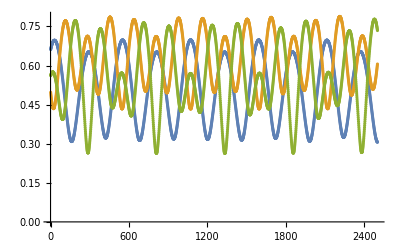

```mathematica
ListPlot[{pn0,pn1,pn2}]
```

```mathematica
points3D=Table[ { pn0[[j]],pn1[[j]],pn2[[j]]},{j,1,Length[pn0]}];
```

```mathematica
mech=ListPointPlot3D[points3D, PlotStyle->Black]
```

-Graphics3D-

#### Second

```mathematica
iniconds=Flatten[Table[{RandomReal[{0,1}],RandomReal[{0,2Pi}]},{3}]]
iniconds[[{1,3,5}]]=Normalize[iniconds[[{1,3,5}]]]^2
ini=Flatten[{Thread[(canVar/.z->0)== iniconds]}]
```

{0.783077,1.28827,0.585903,5.45589,0.355373,1.50332}

{0.566328,0.317037,0.116635}

{n0[0]==0.566328,ϕ0[0]==1.28827,n1[0]==0.317037,ϕ1[0]==5.45589,n2[0]==0.116635,ϕ2[0]==1.50332}

```mathematica
ndeqs=(Flatten[{(deqs/.pars),ini}])
```

{ϕ0'[z]==0.3853+(0.472929 Cos[ϕ0[z]-ϕ1[z]] √n1[z]+0.235346 Cos[ϕ0[z]-ϕ2[z]] √n2[z])/(√n0[z]),n0'[z]==2 √n0[z] (0.472929 √n1[z] Sin[ϕ0[z]-ϕ1[z]]+0.235346 √n2[z] Sin[ϕ0[z]-ϕ2[z]]),ϕ1'[z]==1.08648+(0.472929 Cos[ϕ0[z]-ϕ1[z]] √n0[z]+1.71632 Cos[ϕ1[z]-ϕ2[z]] √n2[z])/(√n1[z]),n1'[z]==2 √n1[z] (-0.472929 √n0[z] Sin[ϕ0[z]-ϕ1[z]]+1.71632 √n2[z] Sin[ϕ1[z]-ϕ2[z]]),ϕ2'[z]==0.633391+(0.235346 Cos[ϕ0[z]-ϕ2[z]] √n0[z]+1.71632 Cos[ϕ1[z]-ϕ2[z]] √n1[z])/(√n2[z]),n2'[z]==-2 √n2[z] (0.235346 √n0[z] Sin[ϕ0[z]-ϕ2[z]]+1.71632 √n1[z] Sin[ϕ1[z]-ϕ2[z]]),n0[0]==0.566328,ϕ0[0]==1.28827,n1[0]==0.317037,ϕ1[0]==5.45589,n2[0]==0.116635,ϕ2[0]==1.50332}

```mathematica
sols=Flatten[NDSolve[ndeqs,canVar,{z,0,100}]]
```

{n0[z]→InterpolatingFunction[{{0., 100.}}, <>][z],ϕ0[z]→InterpolatingFunction[{{0., 100.}}, <>][z],n1[z]→InterpolatingFunction[{{0., 100.}}, <>][z],ϕ1[z]→InterpolatingFunction[{{0., 100.}}, <>][z],n2[z]→InterpolatingFunction[{{0., 100.}}, <>][z],ϕ2[z]→InterpolatingFunction[{{0., 100.}}, <>][z]}

```mathematica
pn0=Table[Sqrt[Chop[n0[z]/.sols]],{z,0,25,0.01}];
pn1=Table[Sqrt[Chop[n1[z]/.sols]],{z,0,25,0.01}];
pn2=Table[Sqrt[Chop[n2[z]/.sols]],{z,0,25,0.01}];
```

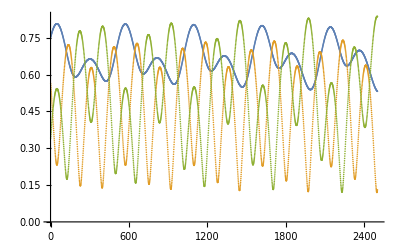

```mathematica
ListPlot[{pn0,pn1,pn2}]
```

```mathematica
points3D=Table[ { pn0[[j]],pn1[[j]],pn2[[j]]},{j,1,Length[pn0]}];
```

```mathematica
mech2=ListPointPlot3D[points3D, PlotStyle->Red]
```

-Graphics3D-

```mathematica
Show[{surface,mech, mech2}]
```

-Graphics3D-

#### third

```mathematica
pars=Thread[Flatten[{ω0,ω1,ω2,g01,g02,g12}->Table[RandomReal[{0,2}],{6}]]]
```

{ω0→1.25032,ω1→1.16405,ω2→1.73596,g01→1.99559,g02→0.457863,g12→1.61207}

```mathematica
iniconds=Flatten[Table[{RandomReal[{0,1}],RandomReal[{0,2Pi}]},{3}]]
iniconds[[{1,3,5}]]=Normalize[iniconds[[{1,3,5}]]]^2
ini=Flatten[{Thread[(canVar/.z->0)== iniconds]}]
```

{0.245566,2.44099,0.679009,3.21746,0.742316,2.75337}

{0.0562322,0.429931,0.513837}

{n0[0]==0.0562322,ϕ0[0]==2.44099,n1[0]==0.429931,ϕ1[0]==3.21746,n2[0]==0.513837,ϕ2[0]==2.75337}

```mathematica
ndeqs=(Flatten[{(deqs/.pars),ini}])
```

{ϕ0'[z]==1.25032+(1.99559 Cos[ϕ0[z]-ϕ1[z]] √n1[z]+0.457863 Cos[ϕ0[z]-ϕ2[z]] √n2[z])/(√n0[z]),n0'[z]==2 √n0[z] (1.99559 √n1[z] Sin[ϕ0[z]-ϕ1[z]]+0.457863 √n2[z] Sin[ϕ0[z]-ϕ2[z]]),ϕ1'[z]==1.16405+(1.99559 Cos[ϕ0[z]-ϕ1[z]] √n0[z]+1.61207 Cos[ϕ1[z]-ϕ2[z]] √n2[z])/(√n1[z]),n1'[z]==2 √n1[z] (-1.99559 √n0[z] Sin[ϕ0[z]-ϕ1[z]]+1.61207 √n2[z] Sin[ϕ1[z]-ϕ2[z]]),ϕ2'[z]==1.73596+(0.457863 Cos[ϕ0[z]-ϕ2[z]] √n0[z]+1.61207 Cos[ϕ1[z]-ϕ2[z]] √n1[z])/(√n2[z]),n2'[z]==-2 √n2[z] (0.457863 √n0[z] Sin[ϕ0[z]-ϕ2[z]]+1.61207 √n1[z] Sin[ϕ1[z]-ϕ2[z]]),n0[0]==0.0562322,ϕ0[0]==2.44099,n1[0]==0.429931,ϕ1[0]==3.21746,n2[0]==0.513837,ϕ2[0]==2.75337}

```mathematica
sols=Flatten[NDSolve[ndeqs,canVar,{z,0,100}]]
```

{n0[z]→InterpolatingFunction[{{0., 100.}}, <>][z],ϕ0[z]→InterpolatingFunction[{{0., 100.}}, <>][z],n1[z]→InterpolatingFunction[{{0., 100.}}, <>][z],ϕ1[z]→InterpolatingFunction[{{0., 100.}}, <>][z],n2[z]→InterpolatingFunction[{{0., 100.}}, <>][z],ϕ2[z]→InterpolatingFunction[{{0., 100.}}, <>][z]}

```mathematica
pn0=Table[Sqrt[Chop[n0[z]/.sols]],{z,0,25,0.01}];
pn1=Table[Sqrt[Chop[n1[z]/.sols]],{z,0,25,0.01}];
pn2=Table[Sqrt[Chop[n2[z]/.sols]],{z,0,25,0.01}];
```

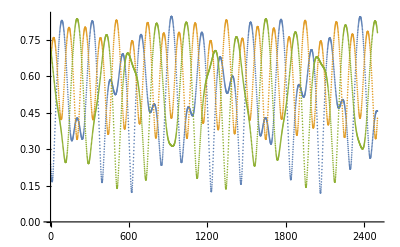

```mathematica
ListPlot[{pn0,pn1,pn2}]
```

```mathematica
points3D=Table[ { pn0[[j]],pn1[[j]],pn2[[j]]},{j,1,Length[pn0]}];
```

```mathematica
mech3=ListPointPlot3D[points3D, PlotStyle->Black]
```

-Graphics3D-

#### fourth

```mathematica
iniconds=Flatten[Table[{RandomReal[{0,1}],RandomReal[{0,2Pi}]},{3}]]
iniconds[[{1,3,5}]]=Normalize[iniconds[[{1,3,5}]]]^2
ini=Flatten[{Thread[(canVar/.z->0)== iniconds]}]
```

{0.92865,4.47524,0.136161,5.56102,0.171865,2.74149}

{0.947195,0.020363,0.0324423}

{n0[0]==0.947195,ϕ0[0]==4.47524,n1[0]==0.020363,ϕ1[0]==5.56102,n2[0]==0.0324423,ϕ2[0]==2.74149}

```mathematica
ndeqs=(Flatten[{(deqs/.pars),ini}])
```

{ϕ0'[z]==1.25032+(1.99559 Cos[ϕ0[z]-ϕ1[z]] √n1[z]+0.457863 Cos[ϕ0[z]-ϕ2[z]] √n2[z])/(√n0[z]),n0'[z]==2 √n0[z] (1.99559 √n1[z] Sin[ϕ0[z]-ϕ1[z]]+0.457863 √n2[z] Sin[ϕ0[z]-ϕ2[z]]),ϕ1'[z]==1.16405+(1.99559 Cos[ϕ0[z]-ϕ1[z]] √n0[z]+1.61207 Cos[ϕ1[z]-ϕ2[z]] √n2[z])/(√n1[z]),n1'[z]==2 √n1[z] (-1.99559 √n0[z] Sin[ϕ0[z]-ϕ1[z]]+1.61207 √n2[z] Sin[ϕ1[z]-ϕ2[z]]),ϕ2'[z]==1.73596+(0.457863 Cos[ϕ0[z]-ϕ2[z]] √n0[z]+1.61207 Cos[ϕ1[z]-ϕ2[z]] √n1[z])/(√n2[z]),n2'[z]==-2 √n2[z] (0.457863 √n0[z] Sin[ϕ0[z]-ϕ2[z]]+1.61207 √n1[z] Sin[ϕ1[z]-ϕ2[z]]),n0[0]==0.947195,ϕ0[0]==4.47524,n1[0]==0.020363,ϕ1[0]==5.56102,n2[0]==0.0324423,ϕ2[0]==2.74149}

```mathematica
sols=Flatten[NDSolve[ndeqs,canVar,{z,0,100}]]
```

{n0[z]→InterpolatingFunction[{{0., 100.}}, <>][z],ϕ0[z]→InterpolatingFunction[{{0., 100.}}, <>][z],n1[z]→InterpolatingFunction[{{0., 100.}}, <>][z],ϕ1[z]→InterpolatingFunction[{{0., 100.}}, <>][z],n2[z]→InterpolatingFunction[{{0., 100.}}, <>][z],ϕ2[z]→InterpolatingFunction[{{0., 100.}}, <>][z]}

```mathematica
pn0=Table[Sqrt[Chop[n0[z]/.sols]],{z,0,25,0.01}];
pn1=Table[Sqrt[Chop[n1[z]/.sols]],{z,0,25,0.01}];
pn2=Table[Sqrt[Chop[n2[z]/.sols]],{z,0,25,0.01}];
```

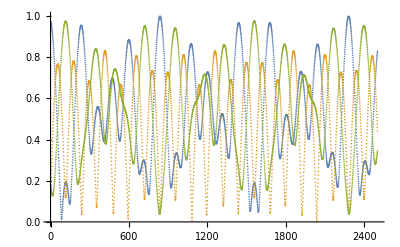

```mathematica
ListPlot[{pn0,pn1,pn2}]
```

```mathematica
points3D=Table[ { pn0[[j]],pn1[[j]],pn2[[j]]},{j,1,Length[pn0]}];
```

```mathematica
mech4=ListPointPlot3D[points3D, PlotStyle->Red]
```

-Graphics3D-

```mathematica
Show[{surface,mech3, mech4}]
```

-Graphics3D-